# Ph3 Set 2

## Jacob Snyder

## 4/3/19



```mathematica
Plot[Sin[x],{x,0,2*Pi}]
```

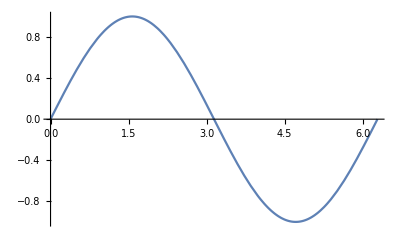

```mathematica
Plot[Sin[x],{x,0,2*Pi},PlotRange->{{0,2*Pi},{-1,1}}]
```

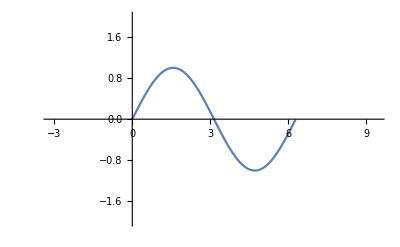

```mathematica
Plot[Sin[x],{x,0,2*Pi},PlotRange->{{-Pi,3*Pi},{-2,2}}]
```

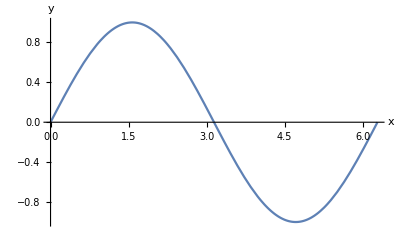

```mathematica
Plot[Sin[x],{x,0,2*Pi},PlotRange->{{0,2*Pi},{-1,1}},AxesLabel->{"x","y"}]
```

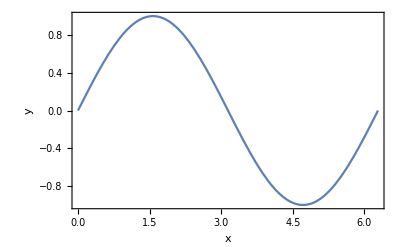

```mathematica
Plot[Sin[x],{x,0,2*Pi},PlotRange->{{0,2*Pi},{-1,1}},AxesLabel->{"x","y"},Frame->True]
```

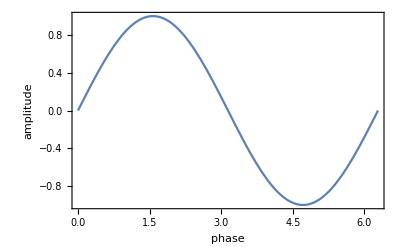

```mathematica
Plot[Sin[x],{x,0,2*Pi},PlotRange->{{0,2*Pi},{-1,1}},AxesLabel->{"x","y"},Frame->True,FrameLabel->{"phase","amplitude"}]
```

```mathematica
Plot3D[Cos[Sqrt[x^2+y^2]]*Exp[-Sqrt[(x^2+y^2)]/5],{x,-5*Pi,5*Pi},{y,-5*Pi,5*Pi},PlotPoints->{100,100},PlotRange->All]
```

-Graphics3D-

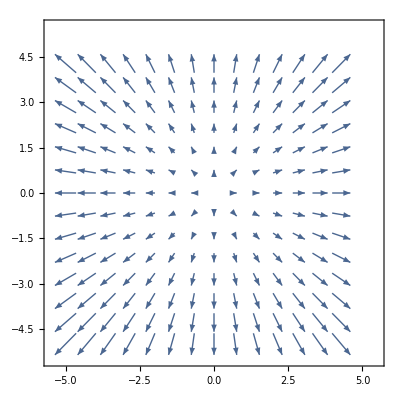

```mathematica
VectorPlot[{x,y},{x,-5,5},{y,-5,5}]
```

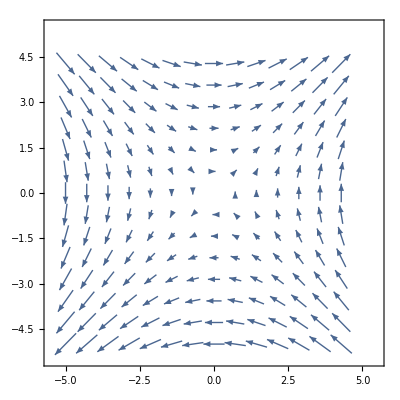

```mathematica
VectorPlot[{y,x},{x,-5,5},{y,-5,5}]
```

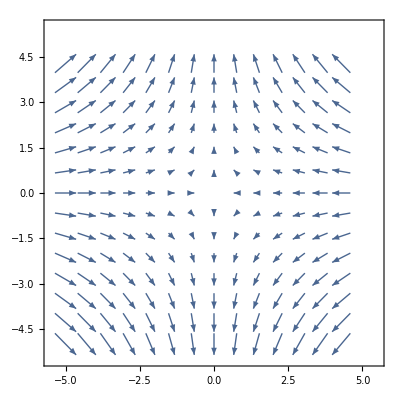

```mathematica
VectorPlot[{-x,y},{x,-5,5},{y,-5,5}]
```

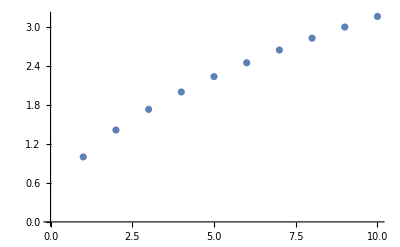

```mathematica
firstten=Table[{i,Sqrt[i]},{i,1,10}];
ListPlot[firstten]
```

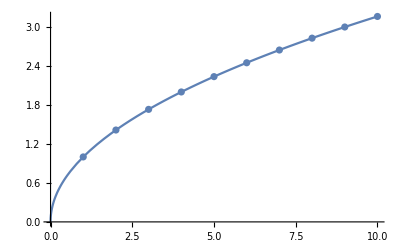

```mathematica
Show[ListPlot[firstten],Plot[Sqrt[x],{x,0,10}]]
```

```mathematica
Needs["ErrorBarPlots`"]
```

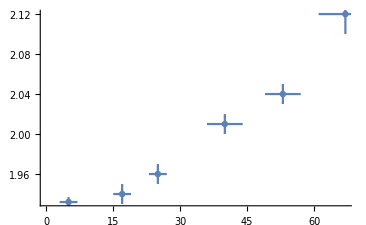

```mathematica
ErrorListPlot[{{{5,1.932},ErrorBar[2,0.005]},{{17,1.94},ErrorBar[2,0.01]},{{25,1.96},ErrorBar[2,0.01]},{{40,2.01},ErrorBar[4,0.01]},{{53,2.04},ErrorBar[4,0.01]},{{67,2.12},ErrorBar[6,0.02]}}]
```